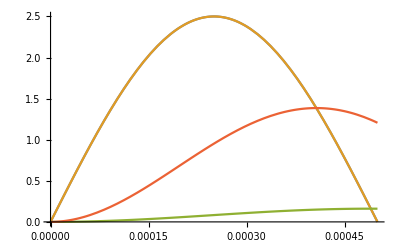

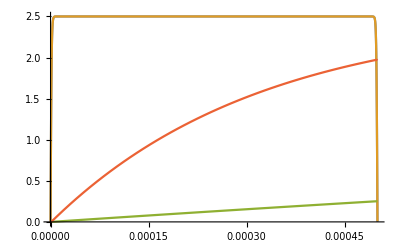

```mathematica
ClearAll["Global`*"]
uzel1=0==iUz[t]+iL[t];
uzel2=iL[t]==iR1[t]+iR2[t];
uzel3=iR1[t]==iC1[t];
uzel4=iR2[t]==iC2[t];

rez1=R1*iR1[t]==u2[t]-u3[t];
rez2=R2*iR2[t]==u2[t]-u4[t];
civka = u1[t]-u2[t]==L*iL'[t];
kond1=iC1[t]==C1*u3'[t];
kond2=iC2[t]==C2*u4'[t];

pp1=iL[0]==0;
pp2=u3[0]==0;
pp3=u4[0]==0;

zdroj = uZ[t]==u1[t];

rovnice={uzel1, uzel2, uzel3, uzel4, rez1, rez2, civka, kond1, kond2, pp1, pp2, pp3, zdroj};

nezname={u1[t], u2[t], u3[t], u4[t], iUz[t], iR1[t], iR2[t], iC1[t], iC2[t], iL[t]};

soucastky= {R1 -> 10*10^3, R2->680, C1-> 470*10^-9, C2->470*10^-9, L->2.2*10^-6};

amplituda= 2.5;
frekvence = 1000;
perioda = 1/frekvence;
tmax=0.5*perioda;
uZ[t_] := amplituda*Sin[2*π*frekvence*t];


Plot[uZ[t],{t,0,tmax}];

reseni = NDSolve[rovnice /. soucastky, nezname,{t,0,tmax}, StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}];

Plot[{u1[t] /. reseni, u2[t] /. reseni, u3[t] /. reseni, u4[t]/.reseni}, {t, 0, tmax}]

uZ[t_] := amplituda*Tanh[100*Sin[2*π*frekvence*t]];

Plot[uZ[t],{t,0,tmax}];

reseni = NDSolve[rovnice /. soucastky, nezname,{t,0,tmax}, StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}];

Plot[{u1[t] /. reseni, u2[t] /. reseni, u3[t] /. reseni, u4[t]/.reseni}, {t, 0, tmax}]
```